```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

```mathematica
A=208;
r0=6.62;(*fm*)
a0=0.546 ;(*fm*)
ρ0=1/NIntegrate[2π r 1/(1+Exp[(r-r0)/a0]),{r,0,∞}];
ws[r_]:=ρ0/(1+Exp[(r-r0)/a0]);
wsp=ProbabilityDistribution[2π r ws[r],{r,0,100}];
```

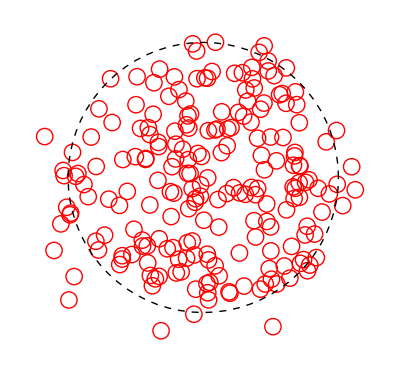

```mathematica
coords=ConstantArray[0,A];
SetSharedVariable[coords];
ParallelDo[coords[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
Graphics[{Table[{Red,Circle[{coords[[i,1]]Cos[coords[[i,2]]],coords[[i,1]]Sin[coords[[i,2]]]},0.4]},{i,1,A,1}],{Dashed,Circle[{0,0},r0]}}]
```

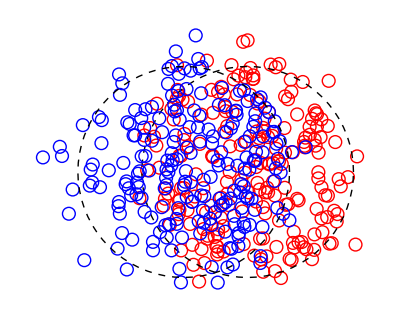

```mathematica
b=4;
coords1=ConstantArray[0,A];
SetSharedVariable[coords1];
ParallelDo[coords1[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords2=ConstantArray[0,A];
SetSharedVariable[coords2];
ParallelDo[coords2[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
Graphics[{Table[{Red,Circle[{coords1[[i,1]]Cos[coords1[[i,2]]]+b/2,coords1[[i,1]]Sin[coords1[[i,2]]]},0.4]},{i,1,A,1}],{Dashed,Circle[{b/2,0},r0]},Table[{Blue,Circle[{coords2[[i,1]]Cos[coords2[[i,2]]]-b/2,coords2[[i,1]]Sin[coords2[[i,2]]]},0.4]},{i,1,A,1}],{Dashed,Circle[{-b/2,0},r0]}}]
```

```mathematica
σ=72;(*mb, at √s=200GeV*)
d=√(σ/π);
```

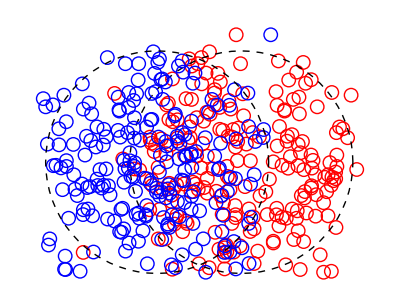

10027

```mathematica
b=5;
coords1=ConstantArray[0,A];
SetSharedVariable[coords1];
ParallelDo[coords1[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords2=ConstantArray[0,A];
SetSharedVariable[coords2];
ParallelDo[coords2[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords1=coords1/.{a_,c_}:>{a Cos[c]+b/2,a Sin[c]};
coords2=coords2/.{a_,c_}:>{a Cos[c]-b/2,a Sin[c]};
Graphics[{Table[{Red,Circle[{coords1[[i,1]],coords1[[i,2]]},0.4]},{i,1,A,1}],{Dashed,Circle[{b/2,0},r0]},Table[{Blue,Circle[{coords2[[i,1]],coords1[[i,2]]},0.4]},{i,1,A,1}],{Dashed,Circle[{-b/2,0},r0]}}]
Ncoll=0;
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,Ncoll=Ncoll+1;],{ii,1,A},{i,1,A}];
Ncoll
```

```mathematica
glauberNcoll[impact_]:=Module[{b=impact,coords1=ConstantArray[0,A],coords2=ConstantArray[0,A],Ncoll=0},
SetSharedVariable[coords1];
SetSharedVariable[coords2];
ParallelDo[coords1[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
ParallelDo[coords2[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords1=coords1/.{a_,c_}:>{a Cos[c]+b/2,a Sin[c]};
coords2=coords2/.{a_,c_}:>{a Cos[c]-b/2,a Sin[c]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,Ncoll=Ncoll+1;],{ii,1,A},{i,1,A}];Return[Ncoll]]
```

```mathematica
bmax=12;
bNcollTab=Table[{impact,glauberNcoll[impact]},{impact,0,bmax,0.5},{i,0,1}];//AbsoluteTiming
```

{156.943,Null}

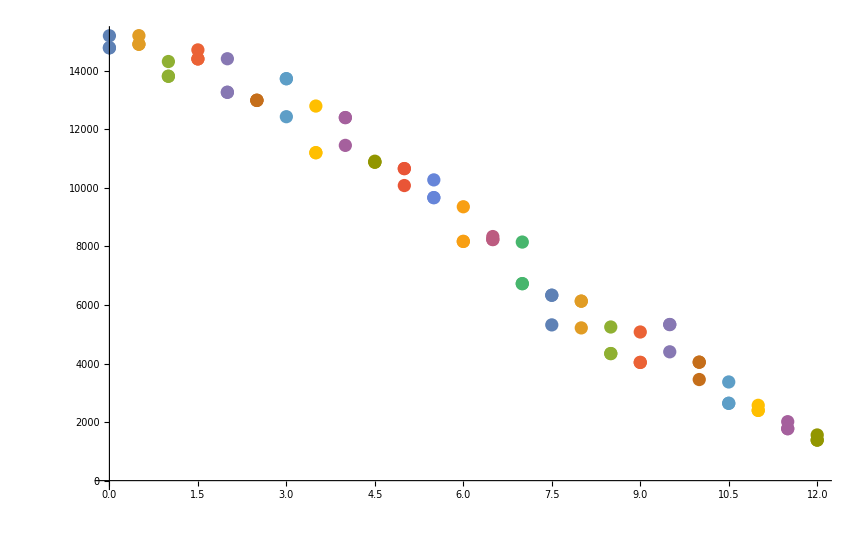

```mathematica
ListPlot[bNcollTab,PlotRange->All]
```

```mathematica
glauberNcoll[impact_]:=Module[{b=impact,coords1=ConstantArray[0,A],coords2=ConstantArray[0,A],Ncoll=0},
SetSharedVariable[coords1];
SetSharedVariable[coords2];
ParallelDo[coords1[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
ParallelDo[coords2[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords1=coords1/.{a_,c_}:>{a Cos[c]+b/2,a Sin[c]};
coords2=coords2/.{a_,c_}:>{a Cos[c]-b/2,a Sin[c]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,Ncoll=Ncoll+1;],{ii,1,A},{i,1,A}];Return[Ncoll]]
```

```mathematica
glauberMCcollcoords[impact_]:=Module[{b=impact,coords1=ConstantArray[0,A],coords2=ConstantArray[0,A],collcoords={},xycoords1,xycoords2},
Do[coords1[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
Do[coords2[[i]]={RandomVariate[wsp],2π RandomReal[]},{i,A}];
coords1=coords1/.{a_,c_}:>{a Cos[c]+b/2,a Sin[c]};
coords2=coords2/.{a_,c_}:>{a Cos[c]-b/2,a Sin[c]};
Do[If[√((coords1[[i,1]]-coords2[[ii,1]])^2+(coords1[[i,2]]-coords2[[ii,2]])^2)≤d,collcoords=Append[Append[collcoords,coords1[[i]]],coords2[[i]]];],{ii,1,A},{i,1,A}];Return[collcoords]];
gauss[x_,x1_,y_,y1_,r_]:=Exp[(-((x-x1)^2+(y-y1)^2))/(2 r^2)];
sumgauss[x_,y_,r_,collcoords_]:=Sum[gauss[x,collcoords[[i,1]],y,collcoords[[i,2]],r],{i,Length[collcoords]}];
```

```mathematica
glauberMCcollcoords[0];//AbsoluteTiming
```

{15.0743,Null}

```mathematica
data=ParallelTable[{b,Table[sumgauss[5,5,1.0,glauberMCcollcoords[b]],{i,0,10}]},{b,0,12,0.5}];//AbsoluteTiming
```

{681.053,Null}

```mathematica
data=data/.{a_,b_}:>{a,Mean[b]};
```

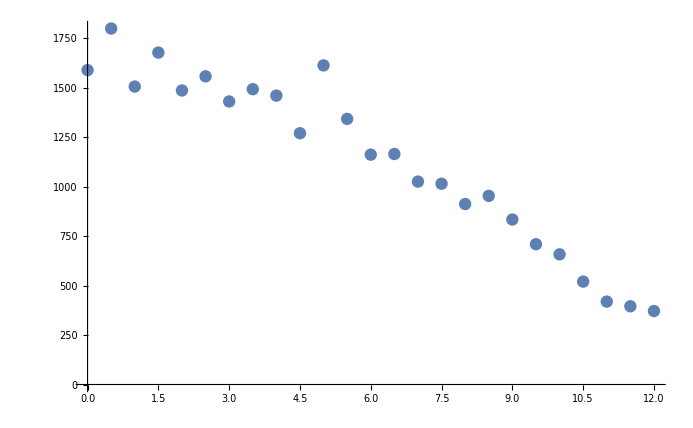

```mathematica
ListPlot[data]
```

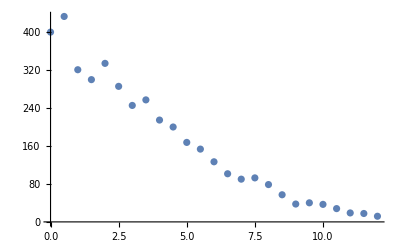

```mathematica
ListPlot[data]
```

```mathematica
Export["ImpactPar00Evolution.dat",data]
```

```mathematica
endeninter[impact_,r_]:=Module[{tab=glauberMCcollcoords[impact]},Interpolation[Flatten[Table[{{x,y},sumgauss[x,y,r,tab]},{x,-6,6,1},{y,-6,6,1}],1]];];
```

```mathematica
DensityPlot[endeninter[0,1.0][x,y],{x,-6,6},{y,-6,6},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

$Aborted